# Lecture 13 - Rotation Wrap-Up

### A Puzzle...

Recall that a 1D mass on a spring has the differential equation

m ẍ=-k x

You can show that the oscillatory solution conserves energy, E=1/2 m (ẋ)^2+1/2 k x^2, by plugging in the explicit form with Sines and Cosines.

However, there is a much easier way to obtain this result. Prove that 1/2 m (ẋ)^2+1/2 k x^2 is a constant value by integrating the equation of motion m ẍ=-k x. (Hint: You will need to multiply both sides by ẋ)

Solution
Multiplying both sides of m ẍ=-k x by ẋ, we can integrate the equation with respect to time,

∫m ẋ ẍ ⅆt=∫-k x ẋ ⅆt

1/2 m (ẋ)^2=-1/2k x^2+C

1/2 m (ẋ)^2+1/2 k x^2=C

Since the left-hand side equals the energy of the system, this equation tells us that energy is conserved with C being determined by initial conditions.

As a sanity check, we can go ahead and also solve this problem by considering the general oscillatory solution

x[t]=A Cos[(k/m)^(1/2)t]+B Sin[(k/m)^(1/2)t]

where A and B are arbitrary variables determined by initial conditions. Substituting this into the energy equation,

E=1/2 m (ẋ)^2+1/2 k x^2
=1/2 m (k/m)(-A Sin[(k/m)^(1/2)t]+B Cos[(k/m)^(1/2)t])^2+1/2 k (A Cos[(k/m)^(1/2)t]+B Sin[(k/m)^(1/2)t])^2
=k (A^2+B^2)

which is conserved, as expected. □

#### Analytical versus Practical

Statistics from 2015: 
Ph 1b was evenly split (134 Anal; 130 in Prac)
Ph 1c was one-sided (86 Anal; 178 Prac)

As you can see, many students switch from Ph 1b Anal to Ph 1c Prac. Here is feedback from two such students, since they give perspective on the two tracks:

"I feel both Prac and Anal require similar time commitments to learn all the material effectively. There will be things in both tracks that people haven’t seen in high school. Additionally, the questions that are chosen for Prac really require a good understanding to get them correct, so it isn’t just an easy A. What I feel it really boils down to is what people want to do with it. If people are going to be engineers and applying this material more than anything I feel Prac does a great job preparing people for that. Also, when you know that is what you’re going to use it for, I believe you put in more effort. Alternatively, if you are looking for a theoretical understanding of physics as a math or physics major (or anyone else who desires it of course), then they should do Anal. The limiting factor for me was that I didn’t really see the light at the end of the tunnel for the anal track when I was taking it, so that stopped me from putting in the time that I would have needed to really get everything."

"I felt Prac took less work and requires less time. Physics majors should take Anal, CS should take Prac. Everyone else should decide for themselves. If you are keenly interested in theory, take Anal. If you just want to get the requirement out of the way, take Prac. Note that the grading curve is much more generous in Prac because all the physics majors (who gladly devote time to this class) are in anal."

My advice:

The most important consideration is how much you enjoy math. If you have a solid calculus background and enjoy integrals, you would like Anal. If you try to avoid integrals at all costs, you should consider Prac (but realize that you will still have to take lots of integrals, although mainly in 1D)

The second most important consideration should be the professor teaching the course. David Hsieh is teaching Anal and Yanbei Chen is teaching Prac. Look at their TQFRs and decide based on their previous teaching. If others have enjoyed their classes in the past, you will too

Lastly, there is a huge boon to taking both Ph 1b Anal and Ph 1c Anal. More precisely, the entire term of Ph 1b Anal builds up to the most incredible calculation you will see in your freshman year, which takes place during the first few weeks of Ph 1c Anal. I guarantee that your mind will be blown!

### Oscillations from a Spring

#### Angled Rails

Example
Two particles of mass m are constrained to move along two rails that make an angle of 2θ with respect to each other, as shown below. They are connected by a spring with spring constant k and unstretched spring length 2 x_0 Sin[θ] where x_0 is the distance along the rails from the base point to one of the masses. Find the frequency of oscillations for the motion where the spring remains parallel to the position (as shown below) if:
1. The two rails are horizontal, so that gravity does not affect the motion
2. The two rails are vertical and gravity does affect the system

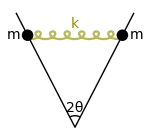

```mathematica
r=0.5;
{pt1,pt2}={{-1,0},{7.2,0}};
pt3=Mean[{pt1,pt2}]+{0,-8};
{pt4,pt5}={{#,Fit[{pt1,pt3},{1,x},x]/.x->#}&[-2],{#,Fit[{pt2,pt3},{1,x},x]/.x->#}&[8.2]};
centerPlot@Show[Graphics[{Line[{pt4,pt3,pt5}],Circle[pt3,1,{ArcTan@@(pt2-pt3),ArcTan@@(pt1-pt3)}],Text[font["2θ"],pt3+{0,1.7}],color2,Text[font["k",Italic],pt3+{0,9}]},ImageSize->150],ParametricPlot[{1/2(-0.8+0.8t+Cos[2t]),1/3 Sin[2t]},{t,-0.8,18.43},PlotStyle->Lighter@color2],Graphics[{Disk[pt1,r],Disk[pt2,r],Text[font["m",Italic],pt1+{-1.2,0}],Text[font["m",Italic],pt2+{1.2,0}]}]]
```

Solution
Denote x to be the distance from the rail intersection at the bottom to a point mass, so that the length of the spring equals 2(x-x_0)Sin[θ] and the spring force is given by -2k (x-x_0)Sin[θ]. Note that the component of the spring force along the rails equals -2k (x-x_0)Sin[θ]^2.

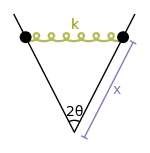

```mathematica
r=0.5;
{pt1,pt2}={{-1,0},{7.2,0}};
pt3=Mean[{pt1,pt2}]+{0,-8};
{pt4,pt5}={{#,Fit[{pt1,pt3},{1,x},x]/.x->#}&[-2],{#,Fit[{pt2,pt3},{1,x},x]/.x->#}&[8.2]};
n1=Normalize[pt2-pt3];
n2={1,-1}*Reverse@n1;
r2=0.3;
centerPlot@Show[Graphics[{Line[{pt4,pt3,pt5}],Circle[pt3,1,{ArcTan@@(pt2-pt3),ArcTan@@(pt1-pt3)}],Text[font["2θ"],pt3+{0,1.7}],color2,Text[font["k",Italic],pt3+{0,9}],color3,Line[{0.95n2+#&/@{pt3,pt2},{(0.95-r2)n2+pt3,(0.95+r2)n2+pt3},{(0.95-r2)n2+pt2,(0.95+r2)n2+pt2}}],Text[font["x",Italic],Mean[0.95n2+#&/@{pt3,pt2}]+{0.7,0}]},ImageSize->150],ParametricPlot[{1/2(-0.8+0.8t+Cos[2t]),1/3 Sin[2t]},{t,-0.8,18.43},PlotStyle->Lighter@color2],Graphics[{Disk[pt1,r],Disk[pt2,r]}]]
```

1. When the rails are horizontal, the motion of the system is dictated purely by the spring force, since gravity points into the page and the normal force only serves to keep the masses on the rails. Thus, F=m a=m ẍ for the system yields

m ẍ=-2k (x-x_0)Sin[θ]^2

Using the natural frequency ω^2=k/m, we can rewrite this as

ẍ=-2 ω^2 (x-x_0)Sin[θ]^2

OverDoubleDot[(x-x_0)]=-2 ω^2 (x-x_0)Sin[θ]^2

where in the last step we used ẍ=OverDoubleDot[(x-x_0)] since the time derivative of the constant x_0 is zero. If we define

(ω̃)^2=2 ω^2 Sin[θ]^2

then Equation (TextNumbered) reduces to

OverDoubleDot[(x-x_0)]=-(ω̃)^2 (x-x_0)

which we know has the solution

x[t]-x_0=c_1 Cos[ω̃ t]+c_2 Cos[ω̃ t]

or equivalently

x[t]=x_0+c_1 Cos[ω̃ t]+c_2 Cos[ω̃ t]

Therefore, the frequency of oscillations is given by

ω̃=((2k)/m)^(1/2)Sin[θ]

2. If the rails are vertical and gravity is in play (with a component m g Cos[θ] along the rails), the sum of the forces equals

m ẍ=-m g Cos[θ]-2k (x-x_0)Sin[θ]^2

Using the frequence ω^2=k/m and reorganizing this equation,

ẍ=-g Cos[θ]-2 ω^2 (x-x_0)Sin[θ]^2

OverDoubleDot[(x-x_0)]+2 ω^2 (x-x_0)Sin[θ]^2=-g Cos[θ]

where, as above, we have used ẍ=OverDoubleDot[(x-x_0)]. If the right-hand side was 0, the solution to this differential equation is given by Equation (TextNumbered). How do we modify this solution to satisfy the current differential equation with the gravity term? As always, we start with the simplest possible guess: can we add a constant to Equation (TextNumbered) and get a valid solution for Equation (TextNumbered)? Indeed, we can, as exhibited by

x[t]=x_0-(g Cos[θ])/(2 ω^2 Sin[θ]^2)+c_1 Cos[ω̃ t]+c_2 Cos[ω̃ t]

Therefore, as we found in the first solution for horizontal rails, the frequency of oscillations is given by

ω̃=((2k)/m)^(1/2)Sin[θ]

This frequency is unchanged between the two cases because gravity exerts a constant force which serves to only shift the equilibrium location of the oscillations (shifting it from being centered on x_0 in the horizontal case to being shifted around x_0-(g Cos[θ])/(2 ω^2 Sin[θ]^2) for the vertical case), but because the spring force is linear the oscillations about this new equilibrium are identical in both cases. □

### Pendulum

#### Supplementary Section: The Basics

Example
A pendulum is comprised of a massless rod of length L which swings a mass m. The mass is brought to angle θ_0 and released from rest. For small oscillations θ_0≪1, what is the period of the resulting motion?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
We can solve the system using force analysis or energy analysis.

Solution 1
We measure positive θ as counter-clockwise. The only forces acting on the mass are T radially towards the pivot point and m g acting straight down.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

In the tangential direction, the only force acting on the mass is gravity m g Sin[θ]. Therefore, F=m a in the tangential acceleration yields

-m g Sin[θ]=m (L θ̈)

(The radial acceleration L (θ̇)^2 is balanced by the tension force, but we won’t need to calculate that.) After canceling m on both sides, we note that for small θ values (θ≪1), we can Taylor expand Sin[θ]=θ+O[θ]^3 to obtain (to first order in θ),

-g θ=L θ̈

Defining ω^2=g/L, we find

θ̈=-ω^2θ

which is exactly the same force that we found for the spring system last time. Therefore, we can use the same solution from last time (in one of its various forms)

θ[t]=A Cos[ω t+ϕ]

Substituting in the initial conditions, A=θ_0 and ϕ=0 so that

θ[t]=θ_0 Cos[ω t]

The mass to oscillate at a frequency ω=(g/L)^(1/2) with a period

T=(2π)/ω=2π (L/g)^(1/2)

This implies that longer pendulum take more time to complete one full revolution, and that changing the length of the rod from l→4l would double the period from T→2T.

When does our solution hold? The only assumption that we made was θ≪1 so that we could approximate Sin[θ]≈θ. We can plot these two functions for the range θ∈[0,π] and see when this approximation is valid.

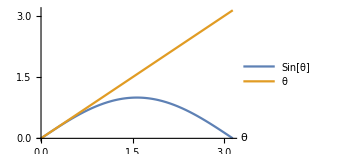

```mathematica
centerPlot@Plot[{Sin[θ],θ},{θ,0,π},AxesLabel->{font@"θ"},PlotLegends->font/@{"Sin[θ]","θ"},ImageSize->250]
```

Thus, we see that it is a reasonable assumption until around θ=0.5radians=30,°.

Solution 2
We can analyze the torques on the pendulum about the pivot point at the top (so that the tension force has a torque of 0 about this point). Therefore, the net torque of the system is due to the gravitational force

τ⃗=r⃗×F⃗=L m g Sin[θ]ẑ

where we have defined the +ẑ direction to point into the page. The angular momentum of the system comes solely from the mass about the (because the rod is massless); the angular momentum about the pivot point equals

L⃗=I ω⃗=-(m L^2) θ̇ ẑ

where the negative sign comes from the fact that when θ̇>0 (i.e. when the pendulum is moving to the right) the angular velocity vector ω⃗ points out of the page. Another way to derive this same result is to use

L⃗=m r⃗×v⃗=-m L (L θ̇)ẑ

where again the minus sign comes from the fact that when θ̇>0 and hence v⃗ points rightward, L⃗ points out of the page. Using τ⃗=(ⅆ L⃗)/ⅆt,

L m g Sin[θ]ẑ=τ⃗=(ⅆ L⃗)/ⅆt=ⅆ/ⅆt[-m L^2 θ̇ ẑ]=-m L^2 θ̈ ẑ

Canceling out m L from both sides and ignoring the ẑ on both sides,

g Sin[θ]=-L θ̈

This is the exact same form found in Solution 1, and the rest of the problem proceeds analogously.

Solution 3
We can consider the pendulum from an energy perspective. The x-coordinate and y-coordinate of the mass are given by

x=L Sin[θ]

y=-L Cos[θ]

Taking time derivatives,

ẋ=L θ̇ Cos[θ]

ẏ=L θ̇ Sin[θ]

Therefore, the velocity squared of the mass is given by

v^2=(ẋ)^2+(ẏ)^2=L^2 (θ̇)^2

Conservation of energy at the initial conditions and at an arbitrary θ yields

m g (-L Cos[θ_0])=1/2 m L^2 (θ̇)^2+m g (-L Cos[θ])

which we can solve for θ̇ as

θ̇=((2g)/L(Cos[θ]-Cos[θ_0]))^(1/2)

Note that in the last step, we have chosen a positive θ̇, which is not true for an entire period of the pendulum’s motion, but is true for half of its period (when it is traveling to the right). However, by symmetry, we know that the exact same motion will happen to the left, and we have not lost anything. Taking another time derivative,

θ̈=1/2((2g)/L(Cos[θ]-Cos[θ_0]))^(-1/2)((2g)/L)(-Sin[θ]θ̇)
=-g/LSin[θ]

where in the last step we have substituted in θ̇. This is the exact same form found in Solution 1, and the rest of the problem proceeds analogously. □

#### Equivalence between a Spring and a Pendulum

In the small angle limit when Sin[θ]≈θ, a horizontal mass on a spring and a simple pendulum become exact analogies of each other (as exhibited by their differential equations having the same form).

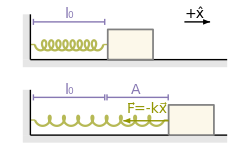
-Graphics- | -Graphics-

```mathematica
r=0.5;
{pt1,pt2}={{-1,0},{7.2,0}};
{t1,t2}={-1.65,25.212};
p1={1/2(0.3t+0.5Cos[2t]),1/3 Sin[2t]}/.t->t1;
p2={1/2(0.3t+0.5Cos[2t]),1/3 Sin[2t]}/.t->t2;
p3=p1+{-0.3,0};
p4=p2+{0.3,0};
x1=-3.;
x2=0.25;
y1=-2.;
x3=0.25+0.15t+1/2(0.3t+0.5Cos[2t])/.t->t2;
x4=(x3+0.3)-(2+First@p4);
plot1=Show[Graphics[{{FaceForm[backgroundColor2],Rectangle[p3+{-0.5,-1},p3+{0,2}],Rectangle[p3+{-0.5,-1.5},p3+{-1,-1}+{x4+12,0}]},Lighter@color2,Line[{{p1,p3},{p2,p4}}],{FaceForm[backgroundColor1],EdgeForm[{Thickness[0.005],Gray}],Rectangle[p4+{0,-1},p4+{3,1}]},{Black,Line[{{p3+{0,-1},p3+{0,2}},{p3+{0,-1},p3+{x4+11,-1}}}]}},ImageSize->250],ParametricPlot[{1/2(0.3t+0.5Cos[2t]),1/3 Sin[2t]},{t,t1,t2},PlotStyle->Lighter@color2],Graphics[{Translate[{{FaceForm[backgroundColor2],Rectangle[p3+{-0.5,-1},p3+{0,2}],Rectangle[p3+{-0.5,-1.5},p3+{-1,-1}+{x4+12,0}]},Lighter@color2,Line[{{p1,p3},{{x3,Last@p2},{x3,Last@p2}+{0.3,0}}}],{FaceForm[backgroundColor1],EdgeForm[{Thickness[0.005],Gray}],Rectangle[{x4+2,0}+p4+{0,-1},{x4+2,0}+p4+{3,1}]},{Black,Line[{{p3+{0,-1},p3+{0,2}},{p3+{0,-1},p3+{x4+11,-1}}}]}},{0,-5}]}],ParametricPlot[{0.25+0.15t+1/2(0.3t+0.5Cos[2t]),-5+1/3 Sin[2t]},{t,t1,t2},PlotStyle->Lighter@color2],Graphics[{{Arrow[#+{0,1.5}&/@{p1+{10+-0.1,0},p1+{11.5+0.1,0}}],Text[font@"+x̂",Mean[{p1+{10+-0.1,0},p1+{11.5+0.1,0}}]+{-0.2,2}]},{color3,Line[#+{0,1.5}&/@{p1+{-0.1,0},p2+{0.1,0}}],Line[{#+{0,1.7},#+{0,1.3}}&/@{p1+{-0.1,0},p2+{0.1,0}}]},Translate[{color3,Line[#+{0,1.5}&/@{p1+{-0.1,0},p2+{0.1,0}}],Line[{#+{0,1.7},#+{0,1.3}}&/@{p1+{-0.1,0},p2+{0.1,0}}]},{0,-5}],Translate[{color3,Line[#+{0,1.5}&/@{p1+{-0.1,0},p2+{x4+0.1,0}-{2.7,0}}],Line[{#+{0,1.7},#+{0,1.3}}&/@{p1+{-0.1,0},p2+{x4+0.1,0}-{2.7,0}}]},{First[p2-p1]+0.35,-5}],{color3,Text[font@"l_0",Mean[{p1,p2}]+{0,2}],Text[font@"l_0",Mean[{p1,p2}]+{0,2}+{0,-5}],Text[font["A",Italic],Mean[{p1,p2}]+{x4/2,2}+{3.4,-5}]},{color2,Thick,Arrowheads[Medium],Arrow[{{x4+2,-5.05}+p4,{x4+2,0}+p4+{-3,-5.05}}],Text[font["F⃗=-kx⃗"],{x4+4.9,-4.25}]}}]];
plot2=-Graphics-;
centerPlot@Grid[{{plot1,plot2}},Spacings->5]
```

The distance x from equilibrium in the spring system translates into a distance L θ in the pendulum system (the arc length that the pendulum has moved from equilibrium). Let us denote this by x↔L θ. We have already found that ω_spring^2=k/m while ω_pendulum^2=g/L, or equivalently k/m↔g/L. Multiplying both sides by m, this implies that the "spring constant" for the pendulum system is effectively k↔(m g)/L. Thus, we have our dictionary to translate any result between a horizontal spring and a simple pendulum

Spring | ↔ | Pendulum
x | ↔ | L θ
k | ↔ | (m g)/L

To see how this can be used, consider the spring system oscillating with x[t]=A Cos[ω_spring t]. When the spring reaches its maximum stretched length x_max=A, all of the energy is in the form of potential energy, E=1/2 k x_max^2. Thus, for a pendulum oscillating with L θ[t]=A Cos[ω_pendulum t], when the pendulum reaches its maximum displacement L θ_max=A, we expect that the energy will be completely in gravitational potential energy E=1/2(m g)/L(L θ)^2=1/2 m g L θ^2. Indeed, we could have found this out directly from the pendulum system, but it requires a Taylor expansion: E=m g h_max=m g (L-L Cos[θ])≈m g ((L θ^2)/2). Using the analogous spring system gives a quick and easy confirmation of this result. With these results, here is an expanded version of our dictionary.

Spring | ↔ | Pendulum
x | ↔ | L θ
k | ↔ | (m g)/L
E=1/2 k x^2 | ↔ | E=1/2(m g)/L(L θ)^2
v=ẋ | ↔ | v=L θ̇

As another application, we can directly turn everything that we learn about a damped and/or driven spring system into the same damped and/or driven pendulum system.

#### Average Tension over a Pendulum Swing

Example
Is the average tension (over one period of oscillation) in the string of a pendulum larger or smaller than m g? By how much? As usual, assume that the angular amplitude A is small.

Solution
The pendulum swings at an angle

θ[t]=A Cos[ω t]

where ω=(g/L)^(1/2). The radial inwards force, the tension minus the radial component of gravity (T-m g Cos[θ]), accounts for the centripetal acceleration (m v^2)/L=(m(θ̇ L))^2/L=m (θ̇)^2 L. Therefore, the tension is given by

T=m g Cos[θ]+m (θ̇)^2 L

We can Taylor expand Cos[θ]≈1-θ^2/2+···, where we keep the second order terms in order to match the second order term m (θ̇)^2 L. Thus

T=m g-1/2 m g θ^2+m (θ̇)^2 L
=m g-1/2 m g A^2 Cos[ω t]^2+m L ω^2 A^2 Sin[ω t]^2
=m g (1-1/2 A^2 Cos[ω t]^2+A^2 Sin[ω t]^2)

Now we need to take the time average (denoted by hard brackets ⟨·⟩) of the right hand side, given by the average value of T over one period of oscillation of the pendulum,

⟨T⟩=1/((2π)/ω)∫_0^(2π/ω) Tⅆt

Rather than integrating directly, we note that over one period,

⟨Cos[ω t]^2⟩=⟨Sin[ω t]^2⟩

In addition,

⟨Cos[ω t]^2+Sin[ω t]^2⟩=⟨1⟩=1

Therefore ⟨Cos[ω t]^2⟩=⟨Sin[ω t]^2⟩=1/2, which we can substitute back into the time average Equation (TextNumbered) to obtain

⟨T⟩=m g (1-1/4 A^2+1/2 A^2)=m g (1+1/4 A^2)

which is larger than m g by 1/4 m g A^2.

It makes sense that T>m g because the average value of the vertical component of T equals m g for small oscillations (as it must, because the pendulum stays has no net rise or fall over a long period of time), and there is some non-zero contribution to the magnitude of T from the horizontal component. □

#### Advanced Section: Better Treatment

So what can we do when the pendulum in the above example is released from a large amplitude such as θ_0=π/2? In such a case, we can proceed as above in the energy solution (Solution 3) to obtain the exact formula

θ̇=((2g)/L(Cos[θ]-Cos[θ_0]))^(1/2)

Writing θ̇=ⅆθ/ⅆt and separating variables, we can integrate along a half period (it must be a half period because we chose the positive sign when taking the square root),

ⅆθ/((2g)/L(Cos[θ]-Cos[θ_0]))^(1/2)=ⅆt

∫_-θ_0^θ_0 ⅆθ/((2g)/L(Cos[θ]-Cos[θ_0]))^(1/2)=∫_0^(T/2) ⅆt

∫_-θ_0^θ_0 ⅆθ/((2g)/L(Cos[θ]-Cos[θ_0]))^(1/2)=T/2

Using the symmetry of the motion as θ increases from -θ_0→0 and 0→θ_0, we can write the period as

T=4∫_0^θ_0 ⅆθ/((2g)/L(Cos[θ]-Cos[θ_0]))^(1/2)

Cos[x] has the very special property that it’s Taylor series exactly equals the original function (provided you include all of the terms in the Taylor series). At this point, we can replace Cos[θ] and Cos[θ_0] by their Taylor series; the more terms that we include, the better our final result will be (i.e. the more higher order terms it will include). Let’s expand to 4th order,

Cos[θ]≈1-θ^2/(2!)+θ^4/(4!)

Cos[θ_0]≈1-θ_0^2/(2!)+θ_0^4/(4!)

so that

Cos[θ]-Cos[θ_0]=1/(2!)(θ_0^2-θ^2)-1/(4!)(θ_0^4-θ^4)
=1/2(θ_0^2-θ^2)(1-1/12(θ_0^2+θ^2))

Our integrand can now be re-written as

1/((2g)/L(Cos[θ]-Cos[θ_0]))^(1/2)≈(L/g)^(1/2)1/((θ_0^2-θ^2)^(1/2))1/((1-1/12(θ_0^2+θ^2))^(1/2))

Using the Taylor series 1/(1-x)^(1/2)=1+x/2+O[x]^2 (which is valid for x≪1, and which we hope is true here),

(L/g)^(1/2)1/((θ_0^2-θ^2)^(1/2))1/((1-1/12(θ_0^2+θ^2))^(1/2))≈(L/g)^(1/2)1/((θ_0^2-θ^2)^(1/2))(1+1/24(θ_0^2+θ^2))

This equation is directly integrable, and using Mathematica we find that the ratio of the original period T_0=2π (L/g)^(1/2) for small oscillations to the new period equals

T=T_0 (1+θ_0^2/16)

```mathematica
T=2π(L/g)^(1/2);
Simplify[1/T Integrate[4*(L/g)^(1/2)1/((θ0^2-θ^2)^(1/2))(1+1/24(θ0^2+θ^2)),{θ,0,θ0}]]
```

1+θ0^2/16

You may be wondering why this method was superior to the last method. After all, we still made an assumption not only by expanding Cos[θ] but also by assuming that 1/12(θ_0^2+θ^2)≪1 in an additional Taylor series. That is true, but in both cases you can continue to include more and more terms in your Taylor series, making progressively better approximations each time. Furthermore, the assumption 1/12(θ_0^2+θ^2)≪1 is much better than the approximation θ≪1 we made previously, since a simple plot shows that it holds for larger ranges of θ.

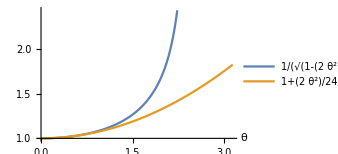

```mathematica
centerPlot@Plot[{1/(√(1-1/12 2*θ^2)),1+1/24 2*θ^2},{θ,0,π},AxesLabel->{font@"θ"},PlotLegends->"Expressions",ImageSize->250]
```

But ultimately, if you really want to calculate higher order terms of the period of a pendulum, you should just use Mathematica. In this case, although the exact period T cannot be written in closed form in terms of trig functions, it can be using elliptic integrals,

```mathematica
T=Integrate[4/Sqrt[(2g)/L(Cos[θ]-Cos[θ0])],{θ,0,θ0}]
```

4 √(L/g) EllipticK[Sin[θ0/2]^2]

Therefore, it is straightforward to ask Mathematica for the ratio of T to T_0=2π (L/g)^(1/2) to any order you like!

```mathematica
T0=2π(L/g)^(1/2);
Tbetter=Series[T/T0,{θ0,0,10}]
```

1+θ0^2/16+(11 θ0^4)/3072+(173 θ0^6)/737280+(22931 θ0^8)/1321205760+(1319183 θ0^10)/951268147200+O[θ0]^11

As we can see below, the period will deviate from the constant value T=2π (L/g)^(1/2) for large angles. As θ_0→π, we expect that the period will go to infinity (since this is an unstable equilibrium point).

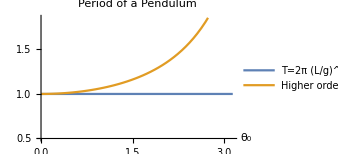

```mathematica
centerPlot@Plot[Evaluate[{1,Normal@Tbetter}],{θ0,0,π},PlotLabel->font@"Period of a Pendulum",AxesLabel->{font["θ_0",12]},PlotLegends->font/@{"T=2π (L/g)^(1/2)","Higher order answer"},AxesOrigin->{0,0.5},Ticks->{Automatic,None},ImageSize->250]
```

#### Neat Examples

There are various neat topics that you can explore with a pendulum. However, these topics are best handled after learning Lagrangian mechanics in the advance Classical Mechanics course. But hopefully the following links will give you a taste for whats out there and an eagerness to learn it!

Pendulum Wave

Can you do the wave? Can you do the pendulum wave?

Spinning Disk

Rotational oscillations, anyone?

Double pendulum

Why stop at one pendulum when you can analyze two? Unlike the motion of a single pendulum, which is periodic, the motion of two pendulums can lead to chaotic motion. However, this very complex motion arises from some very simple looking equations. And in the limit of small oscillations, this system is very well behaved and easy to analyze.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Triple pendulum

Why stop at two? Why stop...at all?

Inverted pendulum

Put a pendulum upside down, and it will predictably fall over. Put a pendulum upside down and then start shaking the base...and you just might find stability!

A pendulum consists of a mass m at the end of a massless stick of length l. The other end of the stick is made to oscillate vertically with a position given y[t]=A Cos[ω t] where A≪l. It turns out that if ω is large enough, and if the pendulum is initially nearly upside-down, then it will surprisingly not fall over as time goes by. Instead, it will (sort of) oscillate back and forth around the vertical position.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

## Mathematica Initialization

```mathematica
$Assumptions=0<θ0<π&&0<Min[g,L]&&By>0&&Bz>0&&c>0&&0<ϕ<2π&&0≤ψ≤2π;
```

```mathematica
T=2π √(L/g);
Tbetter=Simplify[Series[1/T Assuming[0<θ0<π&&0<Min[g,L],Integrate[4/Sqrt[(2g)/L(Cos[θ]-Cos[θ0])],{θ,0,θ0}]],{θ0,0,10}],0<Min[g,L]]
```

```mathematica
(* Primary colors for figures *)
colors={color1,color2,color3,color4,color5,color6}={ColorData[97][1],ColorData[97][10],ColorData[97][5],ColorData[97][6],ColorData[97][9],Lighter[ColorData[97][7],0.2]};
(* Secondar colors for backgrounds *)
backgroundColors={backgroundColor1,backgroundColor2}={RGBColor[0.99, 0.97432, 0.91748],RGBColor[0.9, 0.9, 0.9]};
```

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
(* To make x̂-, ŷ-, and ẑ-direction vectors in a Graphics *)
Clear[directionVectors]
directionVectors[base_,size_:1]:={Black,Arrowheads[Small],Arrow[{{base,base+size{0.1,0}},{base,base+size{0,0.1}},{base,base+size{-0.05,-0.05}}}],Text[font@"x̂",base+size{0.12,0}],Text[font@"ŷ",base+size{0,0.12}],Text[font@"ẑ",base+size{-0.06,-0.065}]}
```